# 1. DN - Računalniška orodja v matematiki

#### 1. Analiza z mathematico

Točke od a do j rešite točno in tudi numerično.

a. Definirajte funkcijo .

```mathematica
f[x_]:=Exp[x+3]/(100 x+2)
```

b. Izračunajte definicijsko območje funkcije .

```mathematica
FunctionDomain[f[x], x]
```

x<-1/50||x>-1/50

c. Izračunajte limite funkcije  na robovih definicijskega območja.

```mathematica
Limit[f[x], x -> -1/50, Direction->"FromAbove"]   
(*leva limita*)

Limit[f[x], x -> -1/50, Direction->"FromBelow"]    (*desna limita*)
```

∞

-∞

d. Izračunajte odvod funkcije .

```mathematica
D[f[x],x]
```

-(100 ⅇ^(3+x))/(2+100 x)^2+ⅇ^(3+x)/(2+100 x)

e. Izračunajte lokalne ekstreme funkcije .

```mathematica
f1[x]:=D[f[x], x]
Solve[f1[x]==0, x]
```

```mathematica
{{x->49/50}} (*lokalni minimum*)
```

ReplaceAll::reps: {x} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

f. Izračunajte intervale naraščanja in padanja funkcije .

```mathematica
criticalPoints=Solve[f1[x]==0,x]
```

{{x→49/50}}

```mathematica
Reduce[f1[x]>0,x,Reals]   (*kje funkcija narašča*)
Reduce[f1[x]<0,x,Reals]   (*kje funkcija pada*)
```

x>49/50

x<-1/50||-1/50<x<49/50

g. Narišite graf funkcije  na intervalu [-5, 5].

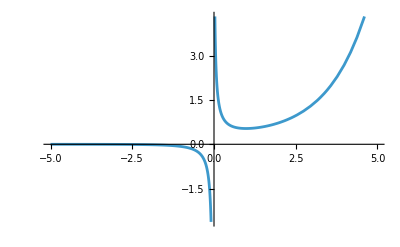

```mathematica
Plot[f[x],{x,-5,5}]
```

h. Določite zalogo vrednosti funkcije .

i. Izračunajte nedoločeni integral funkcije .

j. Na 3 decimalke natančno izračunajte volumen vrtenine , ki jo dobimo, če graf funkcije  zavrtimo okoli  osi na intervalu [0.5, 2]. Vrtenino tudi narišite.

#### 2. Splošno o mathematici

a. Pobrišite vrednost vseh spremenljivk, ki ste jih uporabili v prejšnji nalogi.

b. Definirajte funkcijo  in izračunajte njeno vrednost v vseh celih številih med 1 in 100.

c.  Iz seznama dobljenega v nalogi b. izberite zgolj tiste vrednosti, ki imajo na mestu enic praštevilo. Pomagajte si s _?PrimeQ in MemberQ.

d. Definirajte anonimno funkcijo, ki kvadrira število in mu prišteje 1 in jo uporabite na zgoraj dobljenem seznamu.

e. Seznam iz prejšnje naloge zaokrožite navzdol in seštejte vsa tista števila, ki so deliva s 3.

#### 3. Prepisovalna pravila

```mathematica
Clear[x, y, izraz]
izraz = x^2 + 2x + 1
```

a. Definirajte prepisovalno pravilo, ki  v izrazu vse pojavitve x zamenja z y + 1.

b. Z uporabo prepisovalnih pravil izračunajte vrednost izraza za  x = 2

c. Definirajte funkcija  in s pomočjo prepisovalnih pravil zamenjajte vse pojavitve  v

d. Prepisovalno pravilo iz naloge c uporabite na funkciji ,  kolikokrat gre.

e. Definiraj prepisovalna pravila, s pomočjo katerih lahko izračunate poljuben člen fibonaccijevega zaporedja, z začetkom `Fib[10]`